```mathematica
Quit
```

To loop through the parameter values (ϵ, q_(0,)Ω_m0)  within 1σ and determine if there is corresponding physical trajectories
But: background system only depends on ϵ values, and q(z) depends on ϵ and q_0 values 
--> so need a 2D loop through (ϵ, q_0)

```mathematica
LaunchKernels[];
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
(*Load raw MCMC observables.eps is NOT stored as an independent parameter-it is derived from (q0,j0) via the closure relation.eps_mean from the CSV is kept only as "epsMC" for cross-checking.*)BuildModelParamRanges[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName,mkRange},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
mkRange[base_String]:=Module[{mean,plusErr,minusErr},mean=assocFull[base<>"_mean"];
plusErr=assocFull[base<>"_plus"];
minusErr=assocFull[base<>"_minus"];
<|"mean"->mean,"min"->mean-minusErr,"max"->mean+plusErr|>];
datasetName-><|"q0"->mkRange["q0"],"j0"->mkRange["j0"],"Om0"->mkRange["Om0"],"epsMC"->mkRange["eps"]|>]],rows]]];
```

```mathematica
paramRanges3=BuildModelParamRanges[mcmcFiles["Model 3"]];
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParamRanges[file]],mcmcFiles]];
```

```mathematica
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
planckDatasets={"Planck","Planck + Union3","Planck + Pantheon+","Planck + DESY5","Planck + Union3 + Pantheon+ + DESY5"};
```

## Equations

```mathematica
zPlot=10;
zinitial=1000;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dEh=(1+z)Eh'[z]- Eh[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

Autonomous system of equations
N=-ln(1+z) -> (1+z)d/dz = -d/dN

```mathematica
dxn= x'[n]+(x[n]^2-x[n](2+q[n])-2-2q[n]+3Ω[n])==0;
dΩn=Ω'[n]+Ω[n](x[n]+1-2q[n])==0;
dqn=q'[n]+ (j[n]-q[n]-2 q[n]^2)==0;
djn= j'[n]+ (-s[n]-j[n](2+3q[n]))==0;
dsn=s'[n]+ (-l[n]-s[n](3+4q[n]))==0;
dEhn=Eh'[n]+ Eh[n](1+q[n])==0;
dHn=H'[n]+ H[n](1+q[n])==0;
```

```mathematica
Fx[x_,Ω_,q_]:=-(x^2-x (2+q)-2-2 q+3 Ω);
FΩ[x_,Ω_,q_]:=-Ω (x+1-2 q);
Fq[q_,j_]:=-(j-q-2 q^2);
```

#### Models of j

```mathematica
jModelMap=<|"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

#### Determing ϵ from j0

```mathematica
EpsFast["Model 3",q0_?NumericQ,j0_?NumericQ]:=(j0-1)/(3 (q0-1/2));
```

```mathematica
(*Invert the closure relation at z=0:j0=j_model(q0)->eps.Model 1:eps=(j0-1)/(3(1+q0));Model 2:eps=j0-1;
Model 3:eps=(j0-1)/(3(q0-1/2)).Solve handles all three.*)
EpsFromJ0Q0[model_String,q0Val_?NumericQ,j0Val_?NumericQ]:=
Module[{jExpr,sol},
jExpr=jModelMap[model][n]/. q[n]->q0Val;
sol=Solve[jExpr==j0Val,ϵ];
If[sol==={},Missing["NoSolution"],ϵ/. First[sol]]];
```

```mathematica
Grid[Prepend[Table[With[{q0=paramRanges3[d]["q0"]["mean"],j0=paramRanges3[d]["j0"]["mean"],epsMC=paramRanges3[d]["epsMC"]["mean"]},{d,q0,j0,EpsFromJ0Q0["Model 3",q0,j0],epsMC,EpsFromJ0Q0["Model 3",q0,j0]-epsMC}],{d,AvailableDatasets["Model 3"]}],{"Dataset","q0","j0","ϵ derived","ϵ MCMC mean","difference"}],Frame->All]
```

Dataset | q0 | j0 | ϵ derived | ϵ MCMC mean | difference
DESI | -0.482663 | 0.803388 | 0.0666937 | 0.0667182 | -0.0000244947
Union3 | -0.40775 | 0.627742 | 0.136696 | 0.136757 | -0.0000604528
Pantheon+ | -0.408082 | 0.625476 | 0.137478 | 0.137553 | -0.0000743448
DESY5 | -0.447329 | 0.714331 | 0.100517 | 0.100529 | -0.0000120773
Union3 + Pantheon+ + DESY5 | -0.40875 | 0.621521 | 0.138828 | 0.138852 | -0.0000247859
Planck | -0.638833 | 1.31132 | -0.0911237 | -0.0911274 | 3.64596×10^-6
Planck + Union3 | -0.535124 | 1.04632 | -0.0149176 | -0.0149206 | 2.9356×10^-6
Planck + Pantheon+ | -0.494899 | 0.953345 | 0.0156313 | 0.0156392 | -7.91543×10^-6
Planck + DESY5 | -0.528157 | 1.02938 | -0.00952495 | -0.00952973 | 4.78285×10^-6
Planck + Union3 + Pantheon+ + DESY5 | -0.475607 | 0.909777 | 0.0308262 | 0.0308254 | 7.44127×10^-7

#### Determining q(z)

```mathematica
Options[SolveForq]={"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"MaxSteps"->10^6,"WorkingPrecision"->30};
(*default-zi overload*)
SolveForq[model_String,j0Val_?NumericQ,q0Val_?NumericQ,opts:OptionsPattern[]]:=SolveForq[model,j0Val,q0Val,zinitial,opts];
```

```mathematica
SolveForq[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ,opts:OptionsPattern[]]:=Module[{epsVal,pg,ag,maxSt,wp,sol,qFn,dom},
epsVal=EpsFast[model,q0Val,j0Val];
pg=OptionValue["PrecisionGoal"];
ag=OptionValue["AccuracyGoal"];
maxSt=OptionValue["MaxSteps"];
wp=OptionValue["WorkingPrecision"];
(*Block returns sol;no Return[] inside it*)sol=Block[{q,z},Quiet[NDSolve[{(1+z) q'[z]==((jModelMap[model][z]/. ϵ->epsVal)-q[z]-2 q[z]^2),q[0]==SetPrecision[q0Val,wp]},q,{z,0,zi},PrecisionGoal->pg,AccuracyGoal->ag,MaxSteps->maxSt,WorkingPrecision->wp],{NDSolve::ndsz,NDSolve::mxst,NDSolve::precw,NDSolve::ndtol,NDSolve::nlnum,NDSolve::ndcf}]];
If[!MatchQ[sol,{{__Rule}}],Return[$Failed]];
qFn=Block[{q},q/. sol[[1]]];
dom=qFn["Domain"][[1]];
If[dom[[2]]<zi,Return[$Failed]];
qFn];
```

## Phase Space Analysis:

## Determining stability of fixed points

#### General fixed points for each model and specified dataset

```mathematica
FixedPointsStabilityEps[model_String,epsVal_?NumericQ]:=Module[{jExpr,jAlg,fps,jacMat,jacFn,xx,OO,qq},
jExpr=jModelMap[model][n];
(*substitute onto private symbols:qq,xx,OO cannot collide with the global x,Ω,q used as ODE function names*)jAlg=(jExpr/. q[n]->qq)/. ϵ->epsVal;
fps=NSolve[{Fx[xx,OO,qq]==0,FΩ[xx,OO,qq]==0,Fq[qq,jAlg]==0},{xx,OO,qq},Reals];
jacMat=D[{Fx[xx,OO,qq],FΩ[xx,OO,qq],Fq[qq,jAlg]},{{xx,OO,qq}}];
jacFn=Function[{xv,Ov,qv},jacMat/. {xx->xv,OO->Ov,qq->qv}];
<|"eps"->epsVal,"jAlg"->jAlg,"fixedPoints"->fps,"vars"->{xx,OO,qq},"Jac"->jacFn|>];
```

#### Matter dominated fixed point selection modules

```mathematica
MatterDominatedFPEps[model_String,epsVal_?NumericQ]:=MatterDominatedFPEps[model,epsVal]=Module[{fpResult,fps,vars,Jac,ptVals,target,distances,bestIdx,vals,eig,eigvecs,type},fpResult=FixedPointsStabilityEps[model,epsVal];
fps=fpResult["fixedPoints"];vars=fpResult["vars"];
Jac=fpResult["Jac"];
ptVals=Map[N[vars/. #]&,fps];
target=N[{0,1,1/2}];
distances=Map[Norm[#-target]&,ptVals];
bestIdx=First[Ordering[distances,1]];
vals=ptVals[[bestIdx]];
{eig,eigvecs}=Eigensystem[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
<|"model"->model,"eps"->epsVal,"jAlg"->fpResult["jAlg"],"x"->vals[[1]],"Ω"->vals[[2]],"q"->vals[[3]],"eigenvalues"->eig,"eigenvectors"->eigvecs,"type"->type|>];
```

## Classifying physical trajectories

## Ω_m0 heat map

```mathematica
AMatch[j0Val_?NumericQ,q0Val_?NumericQ]:=Module[{epsVal},epsVal=EpsFromJ0Q0["Model 3",q0Val,j0Val];
(*Model-3 closed form if you want speed:epsVal=(j0Val-1)/(3(q0Val-1/2));*)If[!NumericQ[epsVal],Return[Missing["NoSolution"]]];
(2 (1+q0Val)-3 epsVal)/(3 (1-epsVal))];
```

```mathematica
q0meanPlanck=paramRanges3["Planck"]["q0"]["mean"];
j0meanPlanck=paramRanges3["Planck"]["j0"]["mean"];
```

```mathematica
AMatch[j0meanPlanck, q0meanPlanck]
```

0.304183

```mathematica
(*---band palette:
built as an explicit colour list,evaluated immediately,rather than passed as a named-string ColorFunction option---*)
nBands=12;
bandPalette=ColorData["TemperatureMap"]/@Rescale[Range[nBands],{1,nBands}];
(*swap "TemperatureMap" for "DarkRainbow","SunsetColors","AvocadoColors",etc.*)
```

```mathematica
MakeDatasetPlot[ds_String]:=Module[{q0Mean,j0Mean,om0Min,om0Mean,om0Max,q0Min,q0Max,j0Min,j0Max,q0Pad,j0Pad,q0PlotRange,j0PlotRange,zSample,zLo,zHi,bandEdges,fullEdges,bandColorFunc,heatmap,meanSigmaContours,star,colorbarLegend,styleLegend},

q0Mean=paramRanges3[ds]["q0"]["mean"];
j0Mean=paramRanges3[ds]["j0"]["mean"];
q0Min=paramRanges3[ds]["q0"]["min"];
q0Max=paramRanges3[ds]["q0"]["max"];
j0Min=paramRanges3[ds]["j0"]["min"];
j0Max=paramRanges3[ds]["j0"]["max"];
om0Min=paramRanges3[ds]["Om0"]["min"];
om0Mean=paramRanges3[ds]["Om0"]["mean"];
om0Max=paramRanges3[ds]["Om0"]["max"];

q0Pad=(q0Max-q0Min)/10;
j0Pad=(j0Max-j0Min)/10;
q0PlotRange={q0Min-2 q0Pad,q0Max+2 q0Pad};
j0PlotRange={j0Min-2 j0Pad,j0Max+2 j0Pad};

(*sample AMatch over the plot window to fix band edges*)zSample=Flatten[Table[AMatch[j0Plot,q0Plot],{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]],(j0PlotRange[[2]]-j0PlotRange[[1]])/40},{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]],(q0PlotRange[[2]]-q0PlotRange[[1]])/40}]];

{zLo,zHi}=MinMax[zSample];
bandEdges=Table[zLo+k (zHi-zLo)/nBands,{k,1,nBands-1}];
fullEdges=Join[{zLo},bandEdges,{zHi}];

(*---discrete banded background---*)heatmap=ContourPlot[AMatch[j0Plot,q0Plot],{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]]},{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]]},Contours->bandEdges,ContourShading->bandPalette,ContourLines->None,PlotRangePadding->None,PlotPoints->60];

(*---best-fit+1-sigma branch lines,drawn on top---*)meanSigmaContours=ContourPlot[AMatch[j0Plot,q0Plot],{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]]},{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]]},Contours->{om0Min,om0Mean,om0Max},ContourShading->None,ContourStyle->{Directive[Black,Dashed,Thickness[0.004]],Directive[Black,Thickness[0.006]],Directive[Black,Dashed,Thickness[0.004]]}];
star=Graphics[{Inset[Style["★",24,Black,Bold],{q0Mean,j0Mean}]}];

(*---step function:buckets a value in[zLo,zHi] into its band colour---*)bandColorFunc[s_]:=bandPalette[[Clip[Ceiling[nBands (s-zLo)/(zHi-zLo)],{1,nBands}]]];
colorbarLegend=BarLegend[{bandColorFunc,{zLo,zHi}},Ticks->({#,NumberForm[#,{4,3}]}&/@fullEdges),LegendLabel->"required matched Ωm0",LegendMarkerSize->250];
styleLegend=LineLegend[{Directive[Black,Thickness[0.006]],Directive[Black,Dashed,Thickness[0.004]]},{"best-fit Ωm0 = "<>ToString[om0Mean],"±1σ"}];
Legended[Show[heatmap,meanSigmaContours,star,PlotRange->{q0PlotRange,j0PlotRange},Frame->True,FrameLabel->{"q0","j0"},PlotLabel->"Model 3: "<>ds,ImageSize->300],Placed[Column[{colorbarLegend,styleLegend}],Right]]];
```

```mathematica
datasetPlots=Association[#->MakeDatasetPlot[#]&/@planckDatasets];
```

```mathematica
GraphicsGrid[Partition[Values[datasetPlots],UpTo[3]],ImageSize->1500,Spacings->{40,40}]
```

-Graphics-

```mathematica
MakeDatasetPlot[ds_String]:=Module[{q0Mean,j0Mean,om0Min,om0Mean,om0Max,q0Min,q0Max,j0Min,j0Max,q0Pad,j0Pad,q0PlotRange,j0PlotRange,zSample,zLo,zHi,bandEdges,fullEdges,bandColorFunc,heatmap,meanSigmaContours,paramLines,star,colorbarLegend,styleLegend,q0j0Legend},q0Mean=paramRanges3[ds]["q0"]["mean"];
j0Mean=paramRanges3[ds]["j0"]["mean"];
q0Min=paramRanges3[ds]["q0"]["min"];
q0Max=paramRanges3[ds]["q0"]["max"];
j0Min=paramRanges3[ds]["j0"]["min"];
j0Max=paramRanges3[ds]["j0"]["max"];
om0Min=paramRanges3[ds]["Om0"]["min"];
om0Mean=paramRanges3[ds]["Om0"]["mean"];
om0Max=paramRanges3[ds]["Om0"]["max"];
q0Pad=(q0Max-q0Min)/10;
j0Pad=(j0Max-j0Min)/10;
q0PlotRange={q0Min-2 q0Pad,q0Max+2 q0Pad};
j0PlotRange={j0Min-2 j0Pad,j0Max+2 j0Pad};
zSample=Flatten[Table[AMatch[j0Plot,q0Plot],{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]],(j0PlotRange[[2]]-j0PlotRange[[1]])/40},{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]],(q0PlotRange[[2]]-q0PlotRange[[1]])/40}]];
{zLo,zHi}=MinMax[zSample];
bandEdges=Table[zLo+k (zHi-zLo)/nBands,{k,1,nBands-1}];
fullEdges=Join[{zLo},bandEdges,{zHi}];
(*---discrete banded background,lines off via ContourLines->False---*)heatmap=ContourPlot[AMatch[j0Plot,q0Plot],{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]]},{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]]},Contours->bandEdges,ContourShading->bandPalette,ContourLines->False,PlotRangePadding->None,PlotPoints->60];
(*---best-fit+1-sigma Omegam0 branch lines (black)---*)meanSigmaContours=ContourPlot[AMatch[j0Plot,q0Plot],{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]]},{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]]},Contours->{om0Min,om0Mean,om0Max},ContourShading->None,ContourStyle->{Directive[Black,Dashed,Thickness[0.004]],Directive[Black,Thickness[0.006]],Directive[Black,Dashed,Thickness[0.004]]}];
(*---Jess's q0,j0:solid white at means,dotted white at+/-1sigma---*)paramLines=Graphics[{Directive[White,Thickness[0.006]],Line[{{q0Mean,j0PlotRange[[1]]},{q0Mean,j0PlotRange[[2]]}}],Line[{{q0PlotRange[[1]],j0Mean},{q0PlotRange[[2]],j0Mean}}],Directive[White,Dotted,Thickness[0.005]],Line[{{q0Min,j0PlotRange[[1]]},{q0Min,j0PlotRange[[2]]}}],Line[{{q0Max,j0PlotRange[[1]]},{q0Max,j0PlotRange[[2]]}}],Line[{{q0PlotRange[[1]],j0Min},{q0PlotRange[[2]],j0Min}}],Line[{{q0PlotRange[[1]],j0Max},{q0PlotRange[[2]],j0Max}}]}];
star=Graphics[{Inset[Style["★",24,Black,Bold],{q0Mean,j0Mean}]}];
bandColorFunc[s_]:=bandPalette[[Clip[Ceiling[nBands (s-zLo)/(zHi-zLo)],{1,nBands}]]];
colorbarLegend=BarLegend[{bandColorFunc,{zLo,zHi}},Ticks->({#,NumberForm[#,{4,3}]}&/@fullEdges),LegendLabel->"required matched Ωm0",LegendMarkerSize->200];
styleLegend=LineLegend[{Directive[Black,Thickness[0.006]],Directive[Black,Dashed,Thickness[0.004]]},{"best-fit Ωm0 = "<>ToString[om0Mean],"±1σ"}];
q0j0Legend=LineLegend[{Directive[White,Thickness[0.006]],Directive[White,Dotted,Thickness[0.005]]},{"Jess q0, j0 mean","q0, j0 ±1σ"},Background->GrayLevel[0.8]];
Legended[Show[heatmap,meanSigmaContours,paramLines,star,PlotRange->{q0PlotRange,j0PlotRange},Frame->True,FrameLabel->{"q0","j0"},PlotLabel->"Model 3: "<>ds,ImageSize->330],Placed[Column[{colorbarLegend,styleLegend,q0j0Legend}],Right]]];
```

```mathematica
datasetPlots=Association[#->MakeDatasetPlot[#]&/@planckDatasets];
```

```mathematica
GraphicsGrid[Partition[Values[datasetPlots],UpTo[3]],ImageSize->1600,Spacings->{-10,20}]
```

-Graphics-

## Finding physical trajectories

### Modules

#### Module to classify trajectory viability

```mathematica
(* Trajectory-wide viability classifier Condition:
x/(j-q-2)>=0  (assuming f_R>0),checked along the WHOLE trajectory 

denom = j-q-2;
	tol= 10^-3;

Checks:
1. abs(denom)< tol -> near singular -> denominator vanishing (point is near a fp or coordinate singluarity of (q,j)-> x map);
2. x/denom < 0 -> sign violation (unphysical);
3. Ω≤0 -> Omega violation (unphysical);

else: physical

*)

ClassifyTrajectoryViability[model_String,j0Val_?NumericQ,q0Val_?NumericQ,xFn_,ΩFn_,qFn_,zi_?NumericQ,OptionsPattern[{"NSamples"->150,"SingularTol"->10^-3,"ZMin"->10^-4,"MaxAbsX"->10^3,"MaxOmega"->10,"DomainTol"->10^-8}]]:=Module[{epsVal,nSamples,singTol,zMinSample,maxAbsX,maxOm,domainTol,domain,domainMin,domainMax,zSamples,sampleData,hasSignViolation,hasNearSingular,hasOmegaViolation,hasDivergence,isPhysical,label},
epsVal=EpsFast[model,q0Val,j0Val];
nSamples=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
zMinSample=OptionValue["ZMin"];
maxAbsX=OptionValue["MaxAbsX"];
maxOm=OptionValue["MaxOmega"];
domainTol=OptionValue["DomainTol"];
domain=xFn["Domain"][[1]];
domainMin=domain[[1]];
domainMax=domain[[2]];
(*solution must actually reach z=0 and z=zi-- no extrapolation.DomainTol (strict) judges validity;ZMin only sets sample spacing below.*)If[domainMin>domainTol||domainMax<zi,Return[<|"label"->"Diverged","j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"domainMin"->domainMin,"domainMax"->domainMax,"sampleData"->{}|>]];
zSamples=Prepend[10^Subdivide[Log10[zMinSample],Log10[Min[zi,domainMax]],nSamples-2],0];
sampleData=Table[Module[{xVal,ΩVal,qVal,jVal,denom,ratio,pointLabel},xVal=xFn[zPt];
ΩVal=ΩFn[zPt];
qVal=qFn[zPt];
jVal=(jModelMap[model][zPt]/. ϵ->epsVal)/. q[zPt]->qVal;
denom=jVal-qVal-2;
pointLabel=Which[!(NumericQ[xVal]&&NumericQ[ΩVal]),"Divergent",Abs[xVal]>maxAbsX||ΩVal>maxOm,"Divergent",Abs[denom]<singTol,"NearSingular",ΩVal<=0,"OmegaViolation",xVal/denom<0,"SignViolation",True,"OK"];
ratio=If[Abs[denom]<singTol,Indeterminate,xVal/denom];
<|"z"->zPt,"x"->xVal,"Ω"->ΩVal,"q"->qVal,"j"->jVal,"denom"->denom,"ratio"->ratio,"pointLabel"->pointLabel|>],{zPt,zSamples}];
hasDivergence=AnyTrue[sampleData,#["pointLabel"]==="Divergent"&];
hasNearSingular=AnyTrue[sampleData,#["pointLabel"]==="NearSingular"&];
hasOmegaViolation=AnyTrue[sampleData,#["pointLabel"]==="OmegaViolation"&];
hasSignViolation=AnyTrue[sampleData,#["pointLabel"]==="SignViolation"&];
isPhysical=!(hasDivergence||hasNearSingular||hasOmegaViolation||hasSignViolation);
label=Which[isPhysical,"Physical",hasDivergence,"Divergent",hasNearSingular,"NearSingular",hasOmegaViolation,"OmegaViolation",hasSignViolation,"SignViolation"];
<|"label"->label,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"hasDivergence"->hasDivergence,"hasSignViolation"->hasSignViolation,"hasNearSingular"->hasNearSingular,"hasOmegaViolation"->hasOmegaViolation,"minRatio"->Min[Cases[sampleData[[All,"ratio"]],_?NumericQ]],"minOmega"->Min[sampleData[[All,"Ω"]]],"maxOmega"->Max[sampleData[[All,"Ω"]]],"maxAbsX"->Max[Abs[sampleData[[All,"x"]]]],"minAbsDenom"->Min[Abs[sampleData[[All,"denom"]]]],"domainMin"->domainMin,"domainMax"->domainMax,"sampleData"->sampleData|>];
```

#### Classification of eigenvectors:

```mathematica
(* ClassifyEigenvectors Splits the 2 unstable eigenvectors at the matter-dominated saddle into the one aligned with q (vq) and the one spanning x-Ω (vxOmega),based on which has a near-zero q-component.*)
ClassifyEigenvectors[fp_Association]:=Module[{eig,vecs,unstableIdx,stableIdx,vq,vxOmega,qComponents},
eig=fp["eigenvalues"];
vecs=fp["eigenvectors"];
unstableIdx=Flatten[Position[eig,_?(Re[#]>0&)]];
stableIdx=Flatten[Position[eig,_?(Re[#]<0&)]];
qComponents=vecs[[unstableIdx,3]];
vq=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]];
vxOmega=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]];
<|"vq"->vq,"vxOmega"->vxOmega,"vStable"->vecs[[First[stableIdx]]],"lambdaQ"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]],"lambdaXOmega"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]]|>];
```

#### Scan of ICs

ICs built from the eigenvector decomposition

```mathematica
ScanICs[model_String,j0Val_?NumericQ,q0Val_?NumericQ,c2Range_List,zi_:zinitial,OptionsPattern[{"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"MaxSteps"->10^6,"WorkingPrecision"->30}]]:=Module[{epsVal,nSamp,singTol,pg,ag,maxSt,wp,fp,cl,vq,vxOmega,qFn,deltaQ,c3,results},epsVal=EpsFast[model,q0Val,j0Val];
nSamp=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
pg=OptionValue["PrecisionGoal"];
ag=OptionValue["AccuracyGoal"];
maxSt=OptionValue["MaxSteps"];
wp=OptionValue["WorkingPrecision"];
fp=MatterDominatedFPEps[model,epsVal];
cl=ClassifyEigenvectors[fp];
If[cl===$Failed,Return[Table[<|"c2"->c2,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"label"->"DegenerateFP"|>,{c2,c2Range}]]];
vq=cl["vq"];
vxOmega=cl["vxOmega"];
qFn=SolveForq[model,j0Val,q0Val,zi];
If[qFn===$Failed,Return[Table[<|"c2"->c2,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"label"->"qSolveFailed"|>,{c2,c2Range}]]];
deltaQ=qFn[zi]-fp["q"];
c3=deltaQ/vq[[3]];
results=Table[Module[{xi,Ωi,sol,xFn,ΩFn,viability},xi=fp["x"]+c2 vxOmega[[1]]+c3 vq[[1]];
Ωi=fp["Ω"]+c2 vxOmega[[2]]+c3 vq[[2]];

(*sol=Block[{q},q[zz_]:=qFn[zz];
Quiet[NDSolve[{dx,dΩ,x[zi]==xi,Ω[zi]==Ωi},{x,Ω},{z,0,zi},PrecisionGoal->pg,AccuracyGoal->ag,MaxSteps->maxSt,WorkingPrecision->wp],{NDSolve::ndsz,NDSolve::mxst,NDSolve::precw,NDSolve::ndtol,NDSolve::nlnum,NDSolve::ndcf}]];*)
sol=Block[{q},q[zz_]:=qFn[zz];
Quiet[NDSolve[{dx,dΩ,x[zi]==xi,Ω[zi]==Ωi,WhenEvent[Abs[x[z]]>10^3,"StopIntegration"],WhenEvent[Ω[z]>10,"StopIntegration"],WhenEvent[Ω[z]<0,"StopIntegration"]},{x,Ω},{z,0,zi},PrecisionGoal->pg,AccuracyGoal->ag,MaxSteps->maxSt,WorkingPrecision->wp],{NDSolve::ndsz,NDSolve::mxst,NDSolve::precw,NDSolve::ndtol,NDSolve::nlnum,NDSolve::ndcf}]];

If[!MatchQ[sol,{{__Rule}}],<|"c2"->c2,"xi"->xi,"Ωi"->Ωi,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"label"->"Failed"|>,(xFn=x/. sol[[1]];
ΩFn=Ω/. sol[[1]];
viability=ClassifyTrajectoryViability[model,j0Val,q0Val,xFn,ΩFn,qFn,zi,"NSamples"->nSamp,"SingularTol"->singTol];
Join[<|"c2"->c2,"xi"->xi,"Ωi"->Ωi|>,viability])]],{c2,c2Range}];
results];
```

```mathematica
AutoC2Scale[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ]:=Module[{fp,classified},fp=MatterDominatedFPEps[model,EpsFast[model,q0Val,j0Val]];
classified=ClassifyEigenvectors[fp];
If[classified===$Failed,$Failed,(1+zi)^(-classified["lambdaXOmega"])]];
```

```mathematica
AutoC2Range[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ,OptionsPattern[{"LogSpanBelow"->4,"LogSpanAbove"->2,"NPerSign"->40}]]:=Module[{scale,expMin,expMax,positive},scale=AutoC2Scale[model,j0Val,q0Val,zi];
If[scale===$Failed,Return[$Failed]];
expMin=Log10[scale]-OptionValue["LogSpanBelow"];
expMax=Log10[scale]+OptionValue["LogSpanAbove"];
positive=10^Subdivide[expMin,expMax,OptionValue["NPerSign"]-1];
Join[-Reverse[positive],positive]];
```

```mathematica
(*helper:contiguous index runs of "Physical" points in a results list*)PhysicalRuns[results_List]:=Module[{idx},idx=Flatten[Position[results,r_/;r["label"]==="Physical",{1}]];
If[idx==={},{},Split[idx,#2==#1+1&]]];
```

```mathematica
(*default-zi overload*)
SweepXInitial[model_String,j0Val_?NumericQ,q0Val_?NumericQ,opts:OptionsPattern[]]:=SweepXInitial[model,j0Val,q0Val,zinitial,opts];

SweepXInitial[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ,OptionsPattern[{"NCoarse"->60,"LogSpanBelow"->3,"LogSpanAbove"->2,"NRefine"->100,"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"WorkingPrecision"->30}]]:=Module[{epsVal,nC,nR,nSamp,singTol,pg,ag,wp,coarseRange,nTot,coarseResults,runs,refined,allPts},epsVal=EpsFast[model,q0Val,j0Val];
nC=OptionValue["NCoarse"];
nR=OptionValue["NRefine"];
nSamp=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
pg=OptionValue["PrecisionGoal"];
ag=OptionValue["AccuracyGoal"];
wp=OptionValue["WorkingPrecision"];
coarseRange=AutoC2Range[model,j0Val,q0Val,zi,"NPerSign"->nC,"LogSpanBelow"->OptionValue["LogSpanBelow"],"LogSpanAbove"->OptionValue["LogSpanAbove"]];
If[coarseRange===$Failed,Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"nCoarse"->0,"nRefined"->0,"c2Window"->None,"windows"->{},"table"->{},"note"->"Degenerate fixed point"|>]];
nTot=Length[coarseRange];
coarseResults=ScanICs[model,j0Val,q0Val,coarseRange,zi,"NSamples"->nSamp,"SingularTol"->singTol,"PrecisionGoal"->pg,"AccuracyGoal"->ag,"WorkingPrecision"->wp];
runs=PhysicalRuns[coarseResults];
If[runs==={},Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"nCoarse"->0,"nRefined"->0,"c2Window"->None,"windows"->{},"table"->{},"note"->"No Physical points in coarse pass"|>]];
refined=Table[Module[{lo,hi,rng,res,phys},lo=coarseRange[[Max[1,First[run]-1]]];
hi=coarseRange[[Min[nTot,Last[run]+1]]];
rng=Subdivide[lo,hi,nR-1];
res=ScanICs[model,j0Val,q0Val,rng,zi,"NSamples"->nSamp,"SingularTol"->singTol,"PrecisionGoal"->pg,"AccuracyGoal"->ag,"WorkingPrecision"->wp];
phys=Select[res,#["label"]==="Physical"&];
<|"bracket"->{lo,hi},"nPhysical"->Length[phys],"c2Window"->If[phys==={},None,MinMax[phys[[All,"c2"]]]],"points"->Map[<|"c2"->#["c2"],"xi"->#["xi"],"Ωi"->#["Ωi"],"xToday"->#["sampleData"][[1]]["x"],"ΩToday"->#["sampleData"][[1]]["Ω"]|>&,phys]|>],{run,runs}];
allPts=Flatten[refined[[All,"points"]],1];
<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->Length[allPts]>0,"nCoarse"->Total[Length/@runs],"nRefined"->Length[allPts],"nRuns"->Length[runs],"c2Window"->If[allPts==={},None,MinMax[allPts[[All,"c2"]]]],"windows"->refined[[All,"c2Window"]],"table"->allPts|>];
```

### Sweeping (q_0,j_0) grid:

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/(j0,q0) grid validity"];
```

```mathematica
planckDatasets
```

{Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

#### Modules

```mathematica
Get1SigmaGrid[ds_String,nQ0_Integer:3,nJ0_Integer:3]:=Module[{q0s,j0s},
q0s=Subdivide[paramRanges3[ds]["q0"]["min"],paramRanges3[ds]["q0"]["max"],nQ0-1];
j0s=Subdivide[paramRanges3[ds]["j0"]["min"],paramRanges3[ds]["j0"]["max"],nJ0-1];
Flatten[Table[{q0v,j0v},{q0v,q0s},{j0v,j0s}],1]];
```

```mathematica
(*orders c2 candidates by closeness (in log-magnitude) to the analytic scale,so early-exit tries the most physically likely values first*)OrderByProximityToScale[range_List,scale_?NumericQ]:=SortBy[range,Abs[Log10[Abs[#]]-Log10[scale]]&];
```

```mathematica
(*default-zi overload*)
QuickViabilityCheck[model_String,j0Val_?NumericQ,q0Val_?NumericQ,opts:OptionsPattern[]]:=QuickViabilityCheck[model,j0Val,q0Val,zinitial,opts];
QuickViabilityCheck[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ,OptionsPattern[{"NCoarse"->60,"LogSpanBelow"->3,"LogSpanAbove"->2,"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"MaxSteps"->10^6,"WorkingPrecision"->30,"SearchFromScale"->True,"XCut"->None}]]:=Module[{epsVal,nC,nSamp,singTol,pg,ag,maxSt,wp,fp,cl,vq,vxOmega,qFn,deltaQ,c3,scale,coarseRange,searchRange,nTried,result},epsVal=EpsFast[model,q0Val,j0Val];
nC=OptionValue["NCoarse"];
nSamp=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
pg=OptionValue["PrecisionGoal"];
ag=OptionValue["AccuracyGoal"];
maxSt=OptionValue["MaxSteps"];
wp=OptionValue["WorkingPrecision"];
fp=MatterDominatedFPEps[model,epsVal];
cl=ClassifyEigenvectors[fp];
If[cl===$Failed,Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"c2"->None,"nTried"->0,"note"->"Degenerate fixed point"|>]];
vq=cl["vq"];vxOmega=cl["vxOmega"];
qFn=SolveForq[model,j0Val,q0Val,zi];
If[qFn===$Failed,Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"c2"->None,"nTried"->0,"note"->"q solve failed"|>]];
deltaQ=qFn[zi]-fp["q"];
c3=deltaQ/vq[[3]];
coarseRange=AutoC2Range[model,j0Val,q0Val,zi,"NPerSign"->nC,"LogSpanBelow"->OptionValue["LogSpanBelow"],"LogSpanAbove"->OptionValue["LogSpanAbove"]];
If[coarseRange===$Failed,Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"c2"->None,"nTried"->0,"note"->"Degenerate fixed point"|>]];
scale=AutoC2Scale[model,j0Val,q0Val,zi];
searchRange=If[TrueQ[OptionValue["SearchFromScale"]]&&NumericQ[scale],OrderByProximityToScale[coarseRange,scale],coarseRange];
nTried=0;
result=Catch[Do[nTried++;
Module[{xi,Ωi,sol,xFn,ΩFn,viability},xi=fp["x"]+c2 vxOmega[[1]]+c3 vq[[1]];
Ωi=fp["Ω"]+c2 vxOmega[[2]]+c3 vq[[2]];
sol=Block[{q},q[zz_]:=qFn[zz];
Quiet[NDSolve[{dx,dΩ,x[zi]==xi,Ω[zi]==Ωi,WhenEvent[Abs[x[z]]>10^3,"StopIntegration"],WhenEvent[Ω[z]>10,"StopIntegration"],WhenEvent[Ω[z]<0,"StopIntegration"]},{x,Ω},{z,0,zi},PrecisionGoal->pg,AccuracyGoal->ag,MaxSteps->maxSt,WorkingPrecision->wp],{NDSolve::ndsz,NDSolve::mxst,NDSolve::precw,NDSolve::ndtol,NDSolve::nlnum,NDSolve::ndcf}]];
If[MatchQ[sol,{{__Rule}}],xFn=x/. sol[[1]];
ΩFn=Ω/. sol[[1]];
viability=ClassifyTrajectoryViability[model,j0Val,q0Val,xFn,ΩFn,qFn,zi,"NSamples"->nSamp,"SingularTol"->singTol];
If[viability["label"]==="Physical",Throw[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->True,"c2"->c2,"xi"->xi,"Ωi"->Ωi,"nTried"->nTried|>]]]],{c2,searchRange}];
<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"c2"->None,"nTried"->nTried,"note"->"No Physical point in coarse range"|>];
result];
```

```mathematica
(*QuickSweepGrid[model_String,ds_String,nQ0_:10,nJ0_:10,zi_:zinitial,opts___Rule]:=Association[ParallelTable[pt->QuickViabilityCheck[model,pt[[2]],pt[[1]],zi,opts],{pt,Get1SigmaGrid[ds,nQ0,nJ0]},Method->"FinestGrained"]];*)
QuickSweepGrid[model_String,{q0Min_,q0Max_},{j0Min_,j0Max_},nQ0_:10,nJ0_:10,zi_:zinitial,opts___Rule]:=Association[ParallelTable[pt->QuickViabilityCheck[model,pt[[2]],pt[[1]],zi,opts],{pt,Tuples[{Subdivide[q0Min,q0Max,nQ0-1],Subdivide[j0Min,j0Max,nJ0-1]}]},Method->"FinestGrained"]];
```

```mathematica
DistributeDefinitions[OrderByProximityToScale,QuickViabilityCheck,QuickSweepGrid];
ParallelEvaluate[Length[DownValues[QuickViabilityCheck]]];
```

```mathematica
ViableRegionPlot[gridResults_Association,ds_String]:=Module[{yes,no,groups,styles,markers,labels,keep},yes=Keys[Select[gridResults,TrueQ[#["found"]]&]];
no=Keys[Select[gridResults,!TrueQ[#["found"]]&]];
groups={yes,no};
styles={Black,Black};
markers={{"●",9},{"×",12}};
labels={"Allows for physical trajectories","No physical trajectories found"};
keep=Select[Range[Length[groups]],Length[groups[[#]]]>0&];
If[keep==={},Return[Graphics[{},Frame->True,FrameLabel->{"q0","j0"}]]];
ListPlot[groups[[keep]],PlotStyle->styles[[keep]],PlotMarkers->markers[[keep]],Frame->True,PlotRange->{MinMax[Keys[gridResults][[All,1]]],MinMax[Keys[gridResults][[All,2]]]},PlotRangePadding->Scaled[0.04],FrameLabel->{"q0","j0"},PlotLegends->labels[[keep]],ImageSize->420]];
```

### General:

```mathematica
(*res=QuickSweepGrid["Model 3",{-3/4,-2/5},{1/2,8/5},15,24];
DumpSave[FileNameJoin[{NotebookDirectory[],"viableGridModel3.mx"}],res];*)
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"viableGridModel3.mx"}]];
```

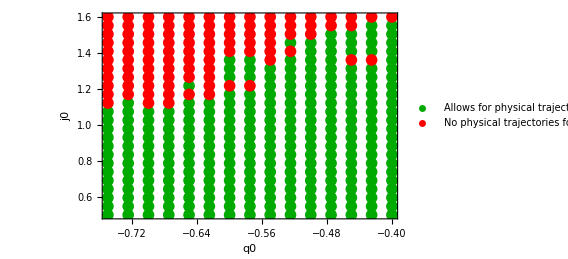

```mathematica
ViableRegionPlot[res,"Model 3"]
```

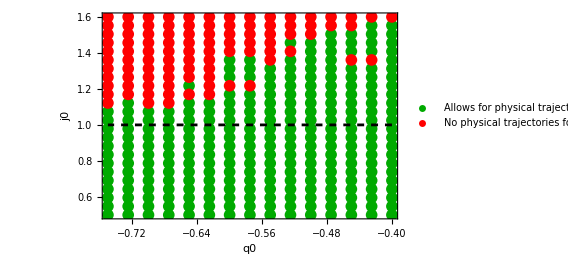

```mathematica
Show[ViableRegionPlot[res,"Model 3"],ContourPlot[EpsFast["Model 3",q0Plot,j0Plot]==0,{q0Plot,-3/4,-2/5},{j0Plot,1/2,8/5},ContourStyle->Directive[Black,Dashed]]]
```

### Datasets

#### Planck

```mathematica
AbsoluteTiming[QuickViabilityCheck["Model 3",j0meanPlanck,q0meanPlanck]]
```

$Aborted

```mathematica
(*planckGridDense=QuickSweepGrid["Model 3","Planck",25,25];//AbsoluteTiming
DumpSave["planckGridDense25x25.mx",planckGridDense];*)
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

{12101.5,Null}

```mathematica
Get["planckGridDense25x25.mx"];
```

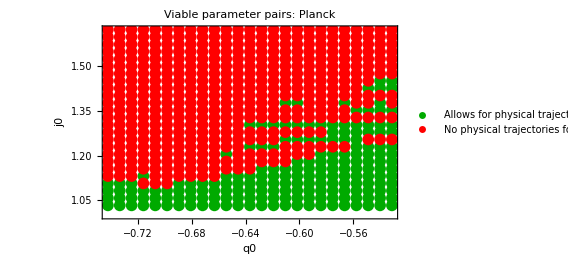

```mathematica
ViableRegionPlot[planckGridDense,"Planck"]
```

#### Planck + Union3

```mathematica
(*name =planckDatasets[[2]]
planck2GridDense=QuickSweepGrid["Model 3",name,20,20];//AbsoluteTiming
DumpSave["planck2GridDense20x20.mx",planck2GridDense];*)
```

Planck + Union3

{2735.38,Null}

```mathematica
name =planckDatasets[[2]];
Get["planck2GridDense20x20.mx"];
```

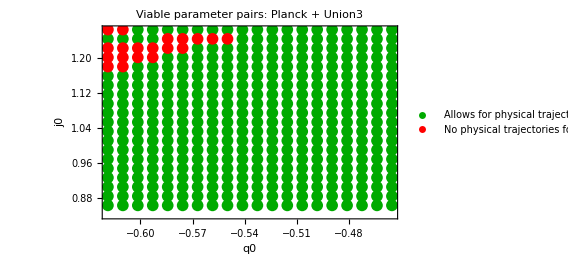

```mathematica
ViableRegionPlot[planck2GridDense,name]
```

#### Planck + Pantheon+

```mathematica
(*name =planckDatasets[[3]]
planck3GridDense=QuickSweepGrid["Model 3",name,20,20];//AbsoluteTiming
DumpSave["planck3GridDense20x20.mx",planck3GridDense];*)
```

Planck + Pantheon+

{1008.56,Null}

```mathematica
name =planckDatasets[[3]];
Get["planck3GridDense20x20.mx"];
```

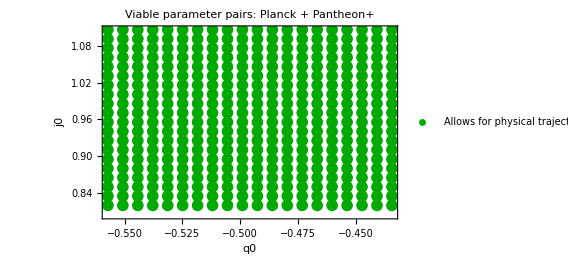

```mathematica
ViableRegionPlot[planck3GridDense,name]
```

#### Planck + DESY5

```mathematica
(*name =planckDatasets[[4]]
planck4GridDense=QuickSweepGrid["Model 3",name,20,20];//AbsoluteTiming
DumpSave["planck4GridDense20x20.mx",planck4GridDense];*)
```

Planck + DESY5

{2002.69,Null}

```mathematica
name =planckDatasets[[4]];
Get["planck4GridDense20x20.mx"];
```

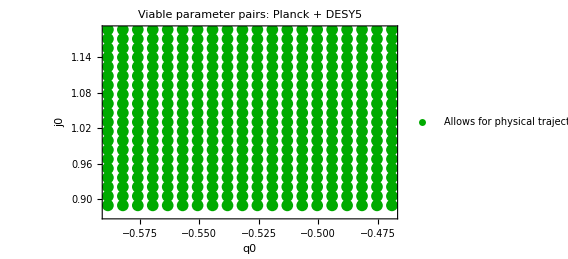

```mathematica
ViableRegionPlot[planck4GridDense,name]
```

#### Planck + Union3 + Pantheon+ + DESY5

```mathematica
(*name =planckDatasets[[5]]
planck5GridDense=QuickSweepGrid["Model 3",name,20,20];//AbsoluteTiming
DumpSave["planck5GridDense20x20.mx",planck5GridDense];*)
```

Planck + Union3 + Pantheon+ + DESY5

{139.444,Null}

```mathematica
name =planckDatasets[[5]];
Get["planck5GridDense20x20.mx"];
```

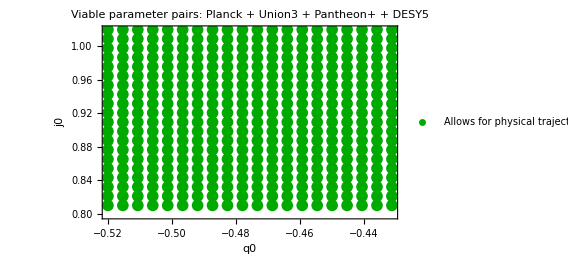

```mathematica
ViableRegionPlot[planck5GridDense,name]
```

```mathematica
gridsByDataset=<|"Planck"->planckGridDense,"Planck + Union3"->planck2GridDense,"Planck + Pantheon+"->planck3GridDense,"Planck + DESY5"->planck4GridDense,"Planck + Union3 + Pantheon+ + DESY5"->planck5GridDense|>;
```

```mathematica
Sweeping (Subscript[q, 0],Subscript[j, 0]) grid:
```

### With |x(0)| restriction

```mathematica
(*everything that depends only on (j0,q0),computed once per grid point*)CutSetup[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ]:=Module[{epsVal,fp,cl,qFn},epsVal=EpsFast[model,q0Val,j0Val];
fp=MatterDominatedFPEps[model,epsVal];
cl=ClassifyEigenvectors[fp];
If[cl===$Failed,Return[$Failed]];
qFn=SolveForq[model,j0Val,q0Val,zi];
If[qFn===$Failed,Return[$Failed]];
<|"model"->model,"j0"->j0Val,"q0"->q0Val,"zi"->zi,"fp"->fp,"vq"->cl["vq"],"vxOmega"->cl["vxOmega"],"qFn"->qFn,"c3"->(qFn[zi]-fp["q"])/cl["vq"][[3]]|>]
```

```mathematica
(*integrate one trajectory for a given c2;same settings as QuickViabilityCheck*)
TrajectoryFromC2[setup_Association,c2_?NumericQ,OptionsPattern[{"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"MaxSteps"->10^6,"WorkingPrecision"->30}]]:=Module[{fp=setup["fp"],vq=setup["vq"],vxO=setup["vxOmega"],qFn=setup["qFn"],c3=setup["c3"],zi=setup["zi"],xi,Ωi,sol,xFn,ΩFn,lab,reaches0},xi=fp["x"]+c2 vxO[[1]]+c3 vq[[1]];
Ωi=fp["Ω"]+c2 vxO[[2]]+c3 vq[[2]];
sol=Block[{q},q[zz_]:=qFn[zz];
Quiet[NDSolve[{dx,dΩ,x[zi]==xi,Ω[zi]==Ωi,WhenEvent[Abs[x[z]]>10^3,"StopIntegration"],WhenEvent[Ω[z]>10,"StopIntegration"],WhenEvent[Ω[z]<0,"StopIntegration"]},{x,Ω},{z,0,zi},PrecisionGoal->OptionValue["PrecisionGoal"],AccuracyGoal->OptionValue["AccuracyGoal"],MaxSteps->OptionValue["MaxSteps"],WorkingPrecision->OptionValue["WorkingPrecision"]],{NDSolve::ndsz,NDSolve::mxst,NDSolve::precw,NDSolve::ndtol,NDSolve::nlnum,NDSolve::ndcf}]];
If[!MatchQ[sol,{{__Rule}}],Return[<|"physical"->False,"x0"->None|>]];
xFn=x/. sol[[1]];ΩFn=Ω/. sol[[1]];
reaches0=Min[xFn["Domain"]]<=0;
lab=ClassifyTrajectoryViability[setup["model"],setup["j0"],setup["q0"],xFn,ΩFn,qFn,zi,"NSamples"->OptionValue["NSamples"],"SingularTol"->OptionValue["SingularTol"]]["label"];
<|"physical"->(lab==="Physical"&&reaches0),"x0"->If[reaches0,xFn[0],None]|>]
```

```mathematica
FindCutC2[setup_Association,c2Found_?NumericQ,xCut_?NumericQ,OptionsPattern[{"h"->10^-3,"MaxMarch"->15,"MaxBisect"->40,"WorkingPrecision"->30}]]:=Catch@Module[{wp=OptionValue["WorkingPrecision"],h=OptionValue["h"],s,traj,pass,fail,t0,tp,tm,dir,good,goodX,bad=None,c2Try,t,mid},s=Abs[c2Found];(*step unit*)traj[c_]:=TrajectoryFromC2[setup,SetPrecision[c,wp]];
pass[c_,tt_]:=<|"pass"->True,"c2"->c,"x0"->tt["x0"]|>;
fail[note_]:=<|"pass"->False,"note"->note,"x0Min"->goodX,"c2Edge"->good|>;
t0=traj[c2Found];
good=c2Found;goodX=t0["x0"];
If[!t0["physical"],Throw[fail["found c2 not reproduced"]]];
If[Abs[t0["x0"]]<=xCut,Throw[pass[c2Found,t0]]];
(*direction in which|x(0)|decreases*)tp=traj[c2Found+h s];tm=traj[c2Found-h s];
dir=Which[tp["physical"]&&tm["physical"],If[Abs[tp["x0"]]<Abs[tm["x0"]],1,-1],tp["physical"],If[Abs[tp["x0"]]<Abs[t0["x0"]],1,-1],tm["physical"],If[Abs[tm["x0"]]<Abs[t0["x0"]],-1,1],True,Throw[fail["window narrower than h"]]];
(*march additively,allowed to cross c2=0*)Do[c2Try=c2Found+dir h 2^k s;t=traj[c2Try];
Which[t["physical"]&&Abs[t["x0"]]<=xCut,Throw[pass[c2Try,t]],t["physical"]&&Abs[t["x0"]]<Abs[goodX],good=c2Try;goodX=t["x0"],t["physical"],Throw[fail["x(0) not monotonic"]],True,bad=c2Try;Break[]],{k,0,OptionValue["MaxMarch"]}];
If[bad===None,Throw[fail["edge not reached"]]];
(*linear bisection between last physical and first non-physical*)Do[mid=(good+bad)/2;t=traj[mid];
Which[t["physical"]&&Abs[t["x0"]]<=xCut,Throw[pass[mid,t]],t["physical"],good=mid;goodX=t["x0"],True,bad=mid],{OptionValue["MaxBisect"]}];
fail["bisection did not reach cut"]]
```

```mathematica
ApplyXCut[model_String,res_,OptionsPattern[{"XCut"->1/4,"zi"->Automatic}]]:=Module[{pts,zi,xCut,n,i=0},xCut=OptionValue["XCut"];
zi=Replace[OptionValue["zi"],Automatic:>zinitial];
pts=Cases[res,a_Association/;KeyExistsQ[a,"found"],{0,Infinity}];
n=Length[pts];
Monitor[Table[i=k;
With[{p=pts[[k]]},If[!TrueQ[p["found"]],Append[p,"status"->"NotViable"],With[{setup=CutSetup[model,p["j0"],p["q0"],zi]},If[setup===$Failed,Join[p,<|"status"->"ViableOnly","cutNote"->"setup failed"|>],With[{r=FindCutC2[setup,p["c2"],xCut]},Join[p,<|"status"->If[TrueQ[r["pass"]],"ViableCut","ViableOnly"],"c2Cut"->Lookup[r,"c2",None],"x0Cut"->Lookup[r,"x0",None],"cutNote"->Lookup[r,"note",None],"x0Min"->Lookup[r,"x0Min",None]|>]]]]]],{k,n}],Row[{"Point ",i," / ",n}]]]
```

```mathematica
Options[PlotXCut]=Join[{"BestFit"->{-0.4756,0.910},"BestFitLabel"->"best fit"},Options[ListPlot]];

PlotXCut[cutRes_List,xCut_:1/4,opts:OptionsPattern[]]:=Module[{spec,data,keep,pts,pad,range,bf,showBF},spec={{"ViableCut",{"●",10},Row[{"viable, |x(0)| ≤ ",N[xCut]}]},{"ViableOnly",{"□",12},Row[{"viable, |x(0)| > ",N[xCut]}]},{"NotViable",{"×",12},"not viable"}};
data=Function[s,Function[p,{p["q0"],p["j0"]}]/@Select[cutRes,Function[p,p["status"]===s]]]/@spec[[All,1]];
keep=Select[Range[3],Length[data[[#]]]>0&];
pts=N@Flatten[data,1];
pad=0.04 (Subtract@@Reverse[MinMax[#]])&/@Transpose[pts];
range={MinMax[pts[[All,1]]]+{-1,1} pad[[1]],MinMax[pts[[All,2]]]+{-1,1} pad[[2]]};
bf=OptionValue["BestFit"];
showBF=MatchQ[bf,{_?NumericQ,_?NumericQ}]&&And@@MapThread[#2[[1]]<=#1<=#2[[2]]&,{bf,range}];
ListPlot[Join[data[[keep]],If[showBF,{{bf}},{}]],FilterRules[{opts},Options[ListPlot]],PlotRange->range,PlotMarkers->Join[spec[[keep,2]],If[showBF,{{"★",18}},{}]],PlotStyle->Join[ConstantArray[Black,Length[keep]],If[showBF,{Blue},{}]],PlotLegends->Join[spec[[keep,3]],If[showBF,{OptionValue["BestFitLabel"]},{}]],Frame->True,ImageSize->500,FrameLabel->{Subscript["q",0],Subscript["j",0]}]]
```

```mathematica
(*cutRes=ApplyXCut["Model 3",res];
DumpSave[FileNameJoin[{NotebookDirectory[],"viableGridModel3Cut.mx"}],cutRes];*)
```

```mathematica
(*resRight=QuickSweepGrid["Model 3",{-3/8,-1/5},{1/2,8/5},8,24];
cutResRight=ApplyXCut["Model 3",resRight];*)
```

```mathematica
(*cutResFull=Join[cutRes,cutResRight];
DumpSave[FileNameJoin[{NotebookDirectory[],"viableGridModel3CutFull.mx"}],cutResFull];*)
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"viableGridModel3Cut.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"viableGridModel3CutFull.mx"}]];
```

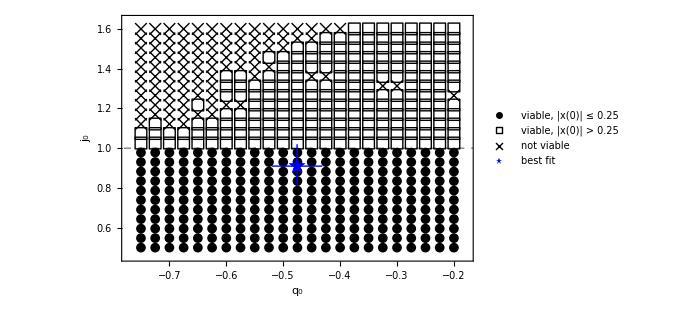

```mathematica
PlotXCut[cutResFull,1/4,Epilog->{Dashed,Gray,InfiniteLine[{{0,1},{1,1}}],Dashing[{}],Blue,AbsoluteThickness[1],Line[{{-0.4756-0.0444,0.910},{-0.4756+0.0443,0.910}}],Line[{{-0.4756,0.910-0.100},{-0.4756,0.910+0.110}}]}]
```

```mathematica
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report figures/Viability/q0_j0_viable_trajectories.png",%206,"PNG"]
```

/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report figures/Viability/q0_j0_viable_trajectories.png

```mathematica
(*(*fine grid across j0=1*)
resFine=QuickSweepGrid["Model 3",{-3/4,-2/5},{19/20,21/20},15,20];
cutResFine=ApplyXCut["Model 3",resFine];
DumpSave[FileNameJoin[{NotebookDirectory[],"viableGridModel3CutFine.mx"}],cutResFine];*)
```

Divide::infy: Infinite expression 1/0 encountered.

NDSolve::nderr: Error test failure at z == 1000.; unable to continue.

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"viableGridModel3CutFine.mx"}]];
```

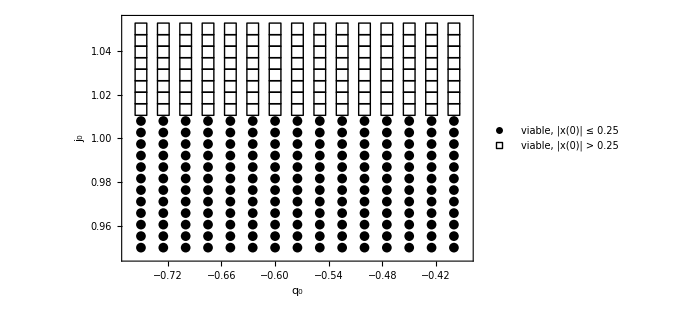

```mathematica
PlotXCut[cutResFine]
```

#### Determinign the effect of the cutoff

```mathematica
BoundaryByQ0[cutRes_List]:=KeyValueMap[{#1,Max[Cases[#2,p_/;p["status"]==="ViableCut":>p["j0"]]],Min[Cases[#2,p_/;p["status"]=!="ViableCut":>p["j0"]]]}&,KeySort@GroupBy[cutRes,#["q0"]&]]
```

```mathematica
TableForm[N@BoundaryByQ0[cutResFine],TableHeadings->{None,{"q0","highest dot j0","lowest non-dot j0"}}]
```

q0 | highest dot j0 | lowest non-dot j0
-0.75 | 1.00789 | 1.01316
-0.725 | 1.00789 | 1.01316
-0.7 | 1.00789 | 1.01316
-0.675 | 1.00789 | 1.01316
-0.65 | 1.00789 | 1.01316
-0.625 | 1.00789 | 1.01316
-0.6 | 1.00789 | 1.01316
-0.575 | 1.00789 | 1.01316
-0.55 | 1.00789 | 1.01316
-0.525 | 1.00789 | 1.01316
-0.5 | 1.00789 | 1.01316
-0.475 | 1.00789 | 1.01316
-0.45 | 1.00789 | 1.01316
-0.425 | 1.00789 | 1.01316
-0.4 | 1.00789 | 1.01316

```mathematica
col=Cases[resFine,a_Association/;KeyExistsQ[a,"found"]&&Abs[a["q0"]+0.475]<10^-6,{0,Infinity}];

Table[{N[xc],BoundaryByQ0[ApplyXCut["Model 3",N[col],"XCut"->xc]]},{xc,{1/10,1/4,1/2}}]
```

{{0.1,{{-19/40,381/380,383/380}}},{0.25,{{-19/40,383/380,77/76}}},{0.5,{{-19/40,387/380,389/380}}}}

```mathematica
N[{{0.1,{{-19/40,381/380,383/380}}},{0.25,{{-19/40,383/380,77/76}}},{0.5,{{-19/40,387/380,389/380}}}}]
```

{{0.1,{{-0.475,1.00263,1.00789}}},{0.25,{{-0.475,1.00789,1.01316}}},{0.5,{{-0.475,1.01842,1.02368}}}}

```mathematica
(*dot/box/cross classification of a single (q0,j0) point*)CutStatus[model_String,q0Val_,j0Val_,xCut_,zi_:zinitial]:=Module[{chk,setup,r},chk=QuickViabilityCheck[model,j0Val,q0Val,zi,"XCut"->None];
If[!TrueQ[chk["found"]],Return["NotViable"]];
setup=CutSetup[model,j0Val,q0Val,zi];
If[setup===$Failed,Return["ViableOnly"]];
r=FindCutC2[setup,chk["c2"],xCut];
If[TrueQ[r["pass"]],"ViableCut","ViableOnly"]]
```

```mathematica
BisectJ0Boundary[model_String,q0Val_,xCut_,{j0Lo_,j0Hi_},tol_:10^-4]:=Module[{lo=j0Lo,hi=j0Hi,mid,sLo,sHi,s,log={}},sLo=CutStatus[model,q0Val,lo,xCut];
sHi=CutStatus[model,q0Val,hi,xCut];
If[sLo=!="ViableCut"||sHi==="ViableCut",Return[<|"xCut"->xCut,"note"->"bracket invalid","statusLo"->sLo,"statusHi"->sHi|>]];
While[hi-lo>tol,mid=(lo+hi)/2;
s=CutStatus[model,q0Val,mid,xCut];
AppendTo[log,{N[mid],s}];
If[s==="ViableCut",lo=mid,hi=mid]];
<|"q0"->N[q0Val],"xCut"->N[xCut],"j0Lo"->N[lo,6],"j0Hi"->N[hi,6],"j0Boundary"->N[(lo+hi)/2,6],"log"->log|>]
```

```mathematica
datasetPaper="Planck + Union3 + Pantheon+ + DESY5";
```

```mathematica
bounds=Table[BisectJ0Boundary["Model 3",paramRanges3[datasetPaper]["q0", "mean"],xc,{99/100,21/20}],{xc,{0.1,0.25,0.5}}];

Dataset[KeyDrop[#,"log"]&/@bounds]
```

```mathematica
Union@@(Last/@#&/@Lookup[bounds,"log"])
```

{ViableCut,ViableOnly}

## Joining source matching and f(R) condition

```mathematica
MakeDatasetPlotViable[ds_String,gridResults_Association,OptionsPattern[{"ShowGridPoints"->False,"MaskContourLines"->True}]]:=Module[{q0Mean,j0Mean,om0Min,om0Mean,om0Max,q0Min,q0Max,j0Min,j0Max,q0Pad,j0Pad,q0PlotRange,j0PlotRange,zSample,zLo,zHi,bandEdges,fullEdges,bandColorFunc,heatmap,meanSigmaContours,star,colorbarLegend,styleLegend,q0sUsed,j0sUsed,foundMatrix,viableInterp,IsViable,gridDots},q0Mean=paramRanges3[ds]["q0"]["mean"];
j0Mean=paramRanges3[ds]["j0"]["mean"];
q0Min=paramRanges3[ds]["q0"]["min"];
q0Max=paramRanges3[ds]["q0"]["max"];
j0Min=paramRanges3[ds]["j0"]["min"];
j0Max=paramRanges3[ds]["j0"]["max"];
om0Min=paramRanges3[ds]["Om0"]["min"];
om0Mean=paramRanges3[ds]["Om0"]["mean"];
om0Max=paramRanges3[ds]["Om0"]["max"];
q0Pad=(q0Max-q0Min)/10;
j0Pad=(j0Max-j0Min)/10;
q0PlotRange={q0Min-2 q0Pad,q0Max+2 q0Pad};
j0PlotRange={j0Min-2 j0Pad,j0Max+2 j0Pad};
(*---build a viable/non-viable test from the dense grid---*)q0sUsed=Union[Keys[gridResults][[All,1]]];
j0sUsed=Union[Keys[gridResults][[All,2]]];
foundMatrix=Table[Boole[TrueQ[gridResults[{q0v,j0v}]["found"]]],{q0v,q0sUsed},{j0v,j0sUsed}];
viableInterp=ListInterpolation[foundMatrix,{q0sUsed,j0sUsed},InterpolationOrder->1];
IsViable[q0v_?NumericQ,j0v_?NumericQ]:=If[q0v<First[q0sUsed]||q0v>Last[q0sUsed]||j0v<First[j0sUsed]||j0v>Last[j0sUsed],False,Quiet[viableInterp[q0v,j0v]]>0.5];
(*---sample AMatch to fix band edges (unchanged)---*)zSample=Flatten[Table[AMatch[j0Plot,q0Plot],{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]],(j0PlotRange[[2]]-j0PlotRange[[1]])/40},{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]],(q0PlotRange[[2]]-q0PlotRange[[1]])/40}]];
{zLo,zHi}=MinMax[zSample];
bandEdges=Table[zLo+k (zHi-zLo)/nBands,{k,1,nBands-1}];
fullEdges=Join[{zLo},bandEdges,{zHi}];
(*---banded background,masked to the viable region---*)heatmap=ContourPlot[AMatch[j0Plot,q0Plot],{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]]},{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]]},Contours->bandEdges,ContourShading->bandPalette,ContourLines->False,PlotRangePadding->None,PlotPoints->60,RegionFunction->Function[{q0Plot,j0Plot},IsViable[q0Plot,j0Plot]]];
(*---Ωm0 mean/1σ lines,masked the same way by default---*)meanSigmaContours=ContourPlot[AMatch[j0Plot,q0Plot],{q0Plot,q0PlotRange[[1]],q0PlotRange[[2]]},{j0Plot,j0PlotRange[[1]],j0PlotRange[[2]]},Contours->{om0Min,om0Mean,om0Max},ContourShading->None,ContourStyle->{Directive[Black,Dashed,Thickness[0.004]],Directive[Black,Thickness[0.006]],Directive[Black,Dashed,Thickness[0.004]]},RegionFunction->If[OptionValue["MaskContourLines"],Function[{q0Plot,j0Plot},IsViable[q0Plot,j0Plot]],Function[{q0Plot,j0Plot},True]]];
star=Graphics[{Inset[Style["★",24,Black,Bold],{q0Mean,j0Mean}]}];
gridDots=If[OptionValue["ShowGridPoints"],Graphics[{PointSize[0.006],KeyValueMap[{If[TrueQ[#2["found"]],Darker[Green],Red],Point[#1]}&,gridResults]}],Graphics[{}]];
bandColorFunc[s_]:=bandPalette[[Clip[Ceiling[nBands (s-zLo)/(zHi-zLo)],{1,nBands}]]];
colorbarLegend=BarLegend[{bandColorFunc,{zLo,zHi}},Ticks->({#,NumberForm[#,{4,3}]}&/@fullEdges),LegendLabel->"required matched Ωm0",LegendMarkerSize->250];
styleLegend=LineLegend[{Directive[Black,Thickness[0.006]],Directive[Black,Dashed,Thickness[0.004]]},{"best-fit Ωm0 = "<>ToString[om0Mean],"±1σ"}];
Legended[Show[heatmap,meanSigmaContours,gridDots,star,PlotRange->{q0PlotRange,j0PlotRange},Frame->True,FrameLabel->{"q0","j0"},PlotLabel->"Model 3: "<>ds<>" (viable region only)",ImageSize->420],Placed[Column[{colorbarLegend,styleLegend}],Right]]];
```

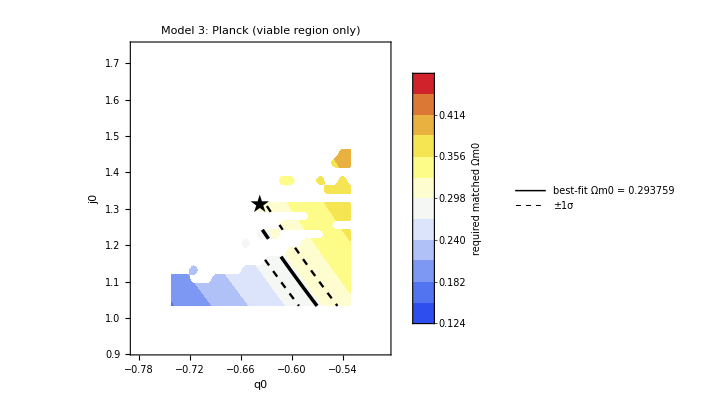

```mathematica
MakeDatasetPlotViable["Planck",planckGridDense]
```

### Check source match viability (Claude)

```mathematica
(*Claude's analysis for checking source matching viability:
SourceMatchTable Purpose: locate,per dataset,a (q0,j0) point satisfying BOTH 
(i)  physical viability-- x/(j-q-2)>=0 along the whole trajectory,established by the grid scan 
(ii) source matching-- AMatch(q0,j0)=Om0(fitted),i.e.the (1+z)^3 coefficient of h^2 equals the fitted matter density (GR recovery at high z) 
These are independent conditions in the same plane;the chosen operating point for the growth analysis should satisfy both.
)
```

```mathematica
SourceMatchTable[datasets_List,grids_Association]:=Module[{rows,hdr},hdr={"Dataset","mean\n(q0, j0)","mean\nviable?","residual\nat mean","viable / total","contour\ncrosses?","residual range","closest\n(q0, j0)","|residual|","offset\n(σ)"};
rows=Table[With[{r=CheckSourceMatchViability[ds,grids[ds]],q0m=paramRanges3[ds]["q0"]["mean"],j0m=paramRanges3[ds]["j0"]["mean"],om0=paramRanges3[ds]["Om0"]["mean"],g=grids[ds]},
Module[{nearKey,meanViable,meanResid,sOm},
(*1-sigma half-width on Om0, to express residuals in units of the observational uncertainty rather than raw Om0 units (asymmetric errors->use half the full span)*)
sOm=(paramRanges3[ds]["Om0"]["max"]-paramRanges3[ds]["Om0"]["min"])/2;
(*THE self-consistency gap at Jess's best-fit point: how far the source-matched Om0 required by (q0,j0) sits from the Om0 the MCMC actually fitted. Zero=>the mean is internally self-consistent.*)
meanResid=AMatch[j0m,q0m]-om0;
(*The MCMC mean is generally NOT a grid node (Subdivide spans min->max,and Jess's errors are asymmetric),so viability at the mean is read off the nearest node.Distances are normalised per axis because q0~-0.5 and j0~1.0 have different scales and spans-- an unnormalised Norm would be dominated by whichever axis happens to be wider.*)nearKey=First[MinimalBy[Keys[g],Norm[{(#[[1]]-q0m)/(paramRanges3[ds]["q0"]["max"]-paramRanges3[ds]["q0"]["min"]),(#[[2]]-j0m)/(paramRanges3[ds]["j0"]["max"]-paramRanges3[ds]["j0"]["min"])}]&]];
meanViable=TrueQ[g[nearKey]["found"]];
{(*---dataset name---*)ds,(*---Jess's MCMC best-fit (q0,j0)---*)Row[{"(",NumberForm[q0m,{4,3}],", ",NumberForm[j0m,{4,3}],")"}],(*---does a physical trajectory exist AT the mean?"no" here means the MCMC best fit cannot be used directly as the operating point (expected for Planck alone)---*)
If[meanViable,Style["yes",Darker[Green],Bold],Style["no",Red,Bold]],(*---residual at the mean,red if it exceeds 1 sigma:a large value means source matching and the MCMC fit disagree at the best-fit point,i.e.the closure relation and the fitted Om0 describe different universes---*)Style[NumberForm[meanResid,{3,4}],If[Abs[meanResid/sOm]>1,Red,Black]],(*---how much of the 1-sigma box admits viable trajectories;
a low fraction (Planck:188/625) means viability is a genuinely restrictive constraint for that dataset---*)If[r["nViable"]===0,"0",ToString[r["nViable"]]<>" / "<>ToString[r["nTotal"]]],(*---THE key column:do the residuals over viable points bracket zero?"yes"=>the source-matching contour passes through the viable region,so a point satisfying BOTH conditions exists."no"=>the two constraints are incompatible for this dataset,which is a result in itself,not a bug---*)Which[r["nViable"]===0,Style["—",Gray],TrueQ[r["crosses"]],Style["yes",Darker[Green],Bold],True,Style["no",Red,Bold]],(*---min-to-max residual across viable points;spanning zero is what "crosses -> yes" is testing---*)If[r["residualRange"]===None,"—",Row[{NumberForm[r["residualRange"][[1]],{3,3}]," to ",NumberForm[r["residualRange"][[2]],{3,3}]}]],(*---CANDIDATE OPERATING POINT:the viable grid node whose source-matched Om0 is closest to the fitted value.This is the point to use for the growth analysis when the mean itself fails (as for Planck)---*)If[r["bestPoint"]===None,"—",Row[{"(",NumberForm[r["bestPoint"][[1]],{4,3}],", ",NumberForm[r["bestPoint"][[2]],{4,3}],")"}]],(*---residual at that closest point.Limited by grid spacing,so this is an upper bound on how well the contour can be resolved,not a physical scale---*)If[r["minAbsResidual"]===None,"—",NumberForm[r["minAbsResidual"],{3,4}]],(*---same residual in units of Jess's 1-sigma Om0 error.Near zero whenever the contour crosses;the informative case is when it does NOT cross,where this quantifies how badly the two constraints miss each other---*)If[r["sigmaOffset"]===None,"—",Style[NumberForm[r["sigmaOffset"],{3,2}],If[Abs[r["sigmaOffset"]]>1,Red,Black]]]}]],{ds,datasets}];
Grid[Prepend[rows,Style[#,Bold]&/@hdr],Frame->All,Alignment->{Join[{Left},ConstantArray[Center,9]],Center},Background->{None,{Lighter[Gray,0.8],None}},Spacings->{1.2,0.8},Dividers->{All,{2->Directive[Thick,Black],All}}]];

SourceMatchTable[planckDatasets,gridsByDataset]
```

Dataset | mean
(q0, j0) | mean
viable? | residual
at mean | viable / total | contour
crosses? | residual range | closest
(q0, j0) | |residual| | offset
(σ)
Planck | (-0.639, 1.311) | yes | 0.0104 | 188 / 625 | yes | -0.115 to 0.106 | (-0.602, 1.132) | 0.0001 | -0.00
Planck + Union3 | (-0.535, 1.046) | yes | 0.0118 | 381 / 400 | yes | -0.086 to 0.109 | (-0.541, 1.011) | 7.0700×10^-6 | -0.00
Planck + Pantheon+ | (-0.495, 0.953) | yes | 0.0123 | 400 / 400 | yes | -0.061 to 0.086 | (-0.544, 1.046) | 3.7500×10^-6 | 0.00
Planck + DESY5 | (-0.528, 1.029) | yes | 0.0119 | 400 / 400 | yes | -0.060 to 0.084 | (-0.525, 0.968) | 0.0000 | -0.00
Planck + Union3 + Pantheon+ + DESY5 | (-0.476, 0.910) | yes | 0.0123 | 400 / 400 | yes | -0.042 to 0.067 | (-0.478, 0.865) | 5.8500×10^-6 | -0.00

## Solving using mean

```mathematica
SweepAllMeans[model_String,datasets_List,zi_:zinitial,opts___Rule]:=Association[Table[ds->Module[{q0m,j0m,res},
q0m=paramRanges3[ds]["q0"]["mean"];
j0m=paramRanges3[ds]["j0"]["mean"];
res=SweepXInitial[model,j0m,q0m,zi,opts];
Join[res,<|"dataset"->ds,"Om0fit"->paramRanges3[ds]["Om0"]["mean"],"Om0source"->AMatch[j0m,q0m]|>]],{ds,datasets}]];
```

```mathematica
planckDatasets
```

{Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
viablePlanckDatasets={"Planck + Union3","Planck + Pantheon+","Planck + DESY5","Planck + Union3 + Pantheon+ + DESY5"};
```

```mathematica
meanSweeps=SweepAllMeans["Model 3",viablePlanckDatasets];//AbsoluteTiming
DumpSave["meanSweeps.mx",meanSweeps];
```

{535.806,Null}

```mathematica
XInitDiagnosticPlot[sweeps_Association,ds_String]:=Module[{res,tbl,xis,xToday,omToday,epsStr,om0fit},res=Lookup[sweeps,ds,Missing["NotRun"]];
tbl=If[AssociationQ[res],Lookup[res,"table",{}],{}];
epsStr=If[AssociationQ[res]&&NumericQ[res["eps"]],ToString[NumberForm[res["eps"],{4,4}]],"?"];
om0fit=paramRanges3[ds]["Om0"]["mean"];
If[!MatchQ[tbl,{__Association}],Return[Graphics[{Text[Style[If[AssociationQ[res],"no viable trajectories","not run"],14,Gray],{0,0}]},Frame->True,FrameTicks->None,ImageSize->420,AspectRatio->0.6,PlotLabel->Style["Model 3, "<>ds,12]]]];
xis=tbl[[All,"xi"]];
xToday=tbl[[All,"xToday"]];
omToday=tbl[[All,"ΩToday"]];
ListPlot[{Transpose[{xis,xToday}],Transpose[{xis,omToday}]},Joined->False,Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(x\), \(i\)]\)",None},PlotRange->{Automatic,{-5,5}},PlotLegends->Placed[{"x(0)","Ω(0)"},{0.9,0.2}],
PlotMarkers->{Automatic,Small},PlotLabel->Style["Model 3, "<>ds,12],ImageSize->420,AspectRatio->0.6]];
```

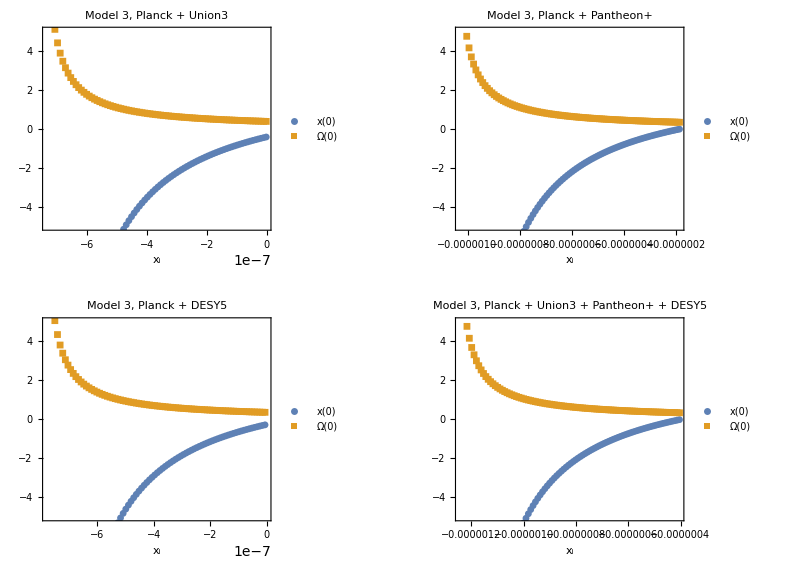

$Aborted

$Aborted

{q0 | highest dot j0 | lowest non-dot j0
-0.75 | 1.00789 | 1.01316
-0.725 | 1.00789 | 1.01316
-0.7 | 1.00789 | 1.01316
-0.675 | 1.00789 | 1.01316
-0.65 | 1.00789 | 1.01316
-0.625 | 1.00789 | 1.01316
-0.6 | 1.00789 | 1.01316
-0.575 | 1.00789 | 1.01316
-0.55 | 1.00789 | 1.01316
-0.525 | 1.00789 | 1.01316
-0.5 | 1.00789 | 1.01316
-0.475 | 1.00789 | 1.01316
-0.45 | 1.00789 | 1.01316
-0.425 | 1.00789 | 1.01316
-0.4 | 1.00789 | 1.01316,BoundaryByQ0[cutResFine10],BoundaryByQ0[cutResFine05]}

```mathematica
GraphicsGrid[Partition[Table[XInitDiagnosticPlot[meanSweeps,ds],{ds,viablePlanckDatasets}],2,2,{1,1},{}],ImageSize->800]
```